## Day1

```mathematica
data=Import["/home/nathan/olin/fall2016/QEAFall2016Homework/inClass/day2/bass1.wav","Data"]
Fs=44100
```

{0.00769066,0.00729392,0.00698874,0.00671407,0.00656148,0.006592,0.00671407,0.00686666,163155,-0.00265503,-0.00250244,-0.00216675,-0.00204468,-0.00186157,-0.00161743,-0.00143433,-0.00106812}
 |  |  |  |

44100

```mathematica
ListPlay[data,SampleRate->Fs]
```

-Graphics-

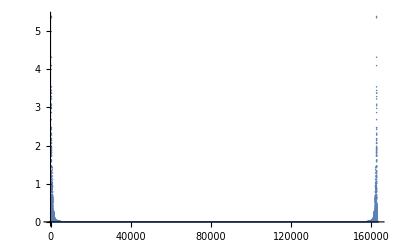

```mathematica
ListPlot[Abs[Fourier[data]],PlotRange->Full]
```

```mathematica
Rasterize@ListLinePlot[RotateRight[Abs[Fourier[data]],Floor@(Length[data]/2)],PlotRange->Full]
```

-Graphics-

```mathematica
Shift[n_]:=(E^(-I*Pi/2*n))
```

```mathematica
shifted=Flatten@MapIndexed[#1*Shift[#2]&,data]
```

{0.-0.00769066 ⅈ,-0.00729392,0.+0.00698874 ⅈ,0.00671407,0.-0.00656148 ⅈ,-0.006592,163159,0.00216675,0.-0.00204468 ⅈ,-0.00186157,0.+0.00161743 ⅈ,0.00143433,0.-0.00106812 ⅈ}
 |  |  |  |

```mathematica
Rasterize@ListLinePlot[RotateRight[Abs[Fourier[shifted]],Floor@(Length[data]/2)],PlotRange->Full]
```

-Graphics-

```mathematica
bandpassShifted=BandpassFilter[shifted,{.4Pi,.6Pi}]
Rasterize@ListLinePlot[RotateRight[Abs[Fourier[bandpassShifted]],Floor@(Length[data]/2)],PlotRange->Full]
```

{-6.51452×10^-19-0.00297718 ⅈ,-0.00363022+0.000766214 ⅈ,3.90149×10^-19+0.00434133 ⅈ,0.00481046-0.000547237 ⅈ,163164,-1.62496×10^-19+0.00117503 ⅈ,0.000961977+0.000106415 ⅈ,1.74924×10^-19-0.000719542 ⅈ}
 |  |  |  |

-Graphics-

```mathematica
Shift2[n_]:=(E^(I*Pi/2*n))
shiftedBack=Flatten@MapIndexed[#1*Shift2[#2]&,bandpassShifted]
```

{0.00297718-6.51452×10^-19 ⅈ,0.00363022-0.000766214 ⅈ,0.00434133-3.90149×10^-19 ⅈ,163165,-0.00117503-1.62496×10^-19 ⅈ,-0.000961977-0.000106415 ⅈ,-0.000719542-1.74924×10^-19 ⅈ}
 |  |  |  |

```mathematica
Rasterize@ListLinePlot[RotateRight[Abs[Fourier[shiftedBack]],Floor@(Length[data]/2)],PlotRange->Full]
```

-Graphics-

```mathematica
ListPlay[shiftedBack,SampleRate->Fs]
```

-Graphics-